```mathematica
(*This notebook creates the MOCHA theory plots,Fig. 2 in the manuscript.*)
```

```mathematica
Get[NotebookDirectory[]<>"23_09_07_3-structure-miniMOCHA-model_1.m"];
```

```mathematica
exampleVals={uCB->0.2,yGM->.9,vNB->.4,B->1,uCL->.01,r->0,vNP->.1,DIN->1,light->30,r->0};
```

```mathematica
VPSColors=RGBColor@@#&/@({{168,68,151},{123,188,73},{231,186,96}}/255);
```

```mathematica
labelsize=30;
tickmargin=5;
```

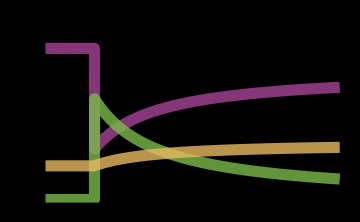

```mathematica
thickness=8;
αStyles={AbsoluteThickness[thickness],#,Opacity[.8]}&/@VPSColors;
αANDjStyle={PlotStyle->αStyles,PlotRangeClipping->False,AxesOrigin->{0,0},ImagePadding->{{60,20},{20,15}},Frame->{{True,True},{True,True}},FrameTicks->{{{#,Row[{"  ",Framed[NumberForm[#,{2,1}],FrameMargins->tickmargin,FrameStyle->None]}],{0,0.02}}&/@Range[0,1,.5],None},{None,None}},LabelStyle->labelsize,ImageSize->Medium,Exclusions->None,Background->Transparent,FrameStyle->({{#,#},{#,#}}&@{{Black,Thick}})};
αStyle=Join[{PlotStyle->αStyles},αANDjStyle];
jPlotLmax=120;
jPlotBmax=2.2 10^6;
letterStyle={FontFamily->"Arial",32};
letterheight=.89;
letterright=.945;
addLetter[letter_,height_]:=(Epilog->Inset[Style[letter,letterStyle],{.95 jPlotLmax,.9 height}])
Clear[αplot];
αplot[pars_,X_,maxX_,options_,letter_]:=Module[{αs,measures},
αs:=(α/.αopt[matrix/.(pars/.{(X->_)->Nothing})]);
Plot[{αs[[1]],αs[[2]],αs[[3]]},{X,0,maxX},Evaluate@options,Evaluate @αStyle,PlotRange->{0,1},(Epilog->Inset[Style[letter,letterStyle],{letterright maxX,letterheight }])]];
αplot1=αplot[exampleVals,light,jPlotLmax,(*FrameLabel->{{"α",""},{"Light",""}}*){FrameLabel->None},"A"]
```

```mathematica
structurenames={
"Vacuoles, α_V",
"Plastids, α_P",
"Growth machinery, α_M"
};
structurenames2={
"Vacuoles",
"Plastids",
"Growth machinery"
};
αplotlegend=Style[Column[
{"Investments",
Grid[Transpose[{Table[Plot[.5,{x,0,1},Axes->None,ImageSize->25,PlotStyle->style],{style,αStyles}],structurenames}],Alignment->Left,Spacings->{1.2,.5}]},Alignment->Center,Spacings->.5],FontFamily->"Arial",labelsize]
```

Investments
-Graphics- | Vacuoles, α_V
-Graphics- | Plastids, α_P
-Graphics- | Growth machinery, α_M

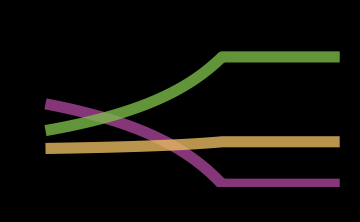

```mathematica
jPlotDINmax=5;
αplot2=αplot[Join[exampleVals],DIN,jPlotDINmax,{FrameTicks->None,AxesLabel->{"DIN"}},"C"]
```

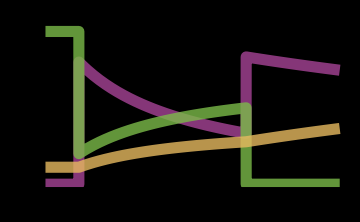

```mathematica
jPlotBmax=2.2;
αplot3=αplot[Join[exampleVals],B,jPlotBmax,{FrameTicks->None,AxesLabel->{"Bact."}},"B"]
```

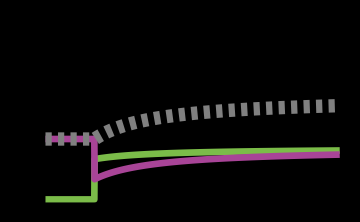

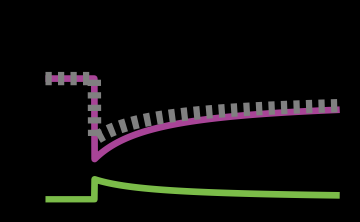

```mathematica
jPlotQuantitiesC={{2,1},1};
jPlotQuantitiesN={{5,4},2};
jColors=Join[{{AbsoluteThickness[thickness],Black}},{AbsoluteThickness[thickness.6],#[[2]](*,AbsoluteDashing[4.5]*)}&/@αStyles[[{2,1}]],{{AbsoluteThickness[thickness 1.2],Gray,AbsoluteDashing[4.5]}}];
jplotStyles=Join[{PlotStyle->jColors,FrameTicks->{{{#,Row[{"  ",Framed[NumberForm[#,{2,1}],FrameMargins->tickmargin,FrameStyle->None]}],{0,0.02}}&/@Range[0,.5,.2],None},{None,None}}},αANDjStyle/.((PlotStyle->_)->Nothing)/.((Exclusions->_)->Nothing)(*,αANDjStyle*)];
(*jplot[pars0_,X_,maxX_,options_,quantities_]:=Module[{(*αoptEvaluate=αopt[matrix],*)αs,measures,pars=pars0/.{(X->_)->Nothing}},
αs:=(α/.αopt[matrix/.pars]);
Plot[Join[
Flatten[matrix.αs/.pars][[{3}]],
Flatten[# Flatten[αs]&/@(matrix)/.pars][[quantities[[1]]]],
Flatten[matrix.αs/.pars][[{quantities[[2]]}]]
],{X,0,maxX},Evaluate@options,Evaluate@jplotStyles,PlotRange->{0,.55}]];*)
jplot[pars0_,X_,maxX_,options_,quantities_,letter_]:=Module[{αs,measures,pars=pars0/.{(X->_)->Nothing},list},
αs:=(α/.αopt[matrix/.pars]);
list=Transpose[Table[{N@X,#}&/@Flatten@{
(matrix.αs/.pars)[[{3}]],
Flatten[# αs&/@(matrix)/.pars][[quantities[[1]]]],
Flatten[matrix.αs/.pars][[{quantities[[2]]}]]
},{X,0,maxX,maxX/1000}]];
ListPlot[list,Joined->True,Evaluate@options,Evaluate@jplotStyles,(Epilog->Inset[Style[letter,letterStyle],{letterright maxX,letterheight .5 }])]];
jplot1C=jplot[exampleVals,light,jPlotLmax,{PlotRange->{0,.5}},jPlotQuantitiesC,"D"]
jplot1N=jplot[exampleVals,light,jPlotLmax,{PlotRange->{0,.5}},jPlotQuantitiesN,"G"]
```

```mathematica
fluxnames=structurenames2[[1;;2]]~Join~{"Total"}~Join~{"Growth"};
jplotlegends=Style[Column[{Style[#[[1]],Bold],Grid[Transpose[{Table[Plot[.5,{x,0,1},Axes->None,ImageSize->25,PlotStyle->style],{style,jColors[[{2,3,4,1}]]}],#[[2]](*{"j_C","j_N","g"}*)}],Alignment->Left,Spacings->1.2]},Alignment->Center,Spacings->.5],FontFamily->"Arial",labelsize]&/@{
{"Carbon fluxes",fluxnames},{"Nitrogen fluxes",fluxnames}}
```

{Carbon fluxes
-Graphics- | Vacuoles
-Graphics- | Plastids
-Graphics- | Total
-Graphics- | Growth,Nitrogen fluxes
-Graphics- | Vacuoles
-Graphics- | Plastids
-Graphics- | Total
-Graphics- | Growth}

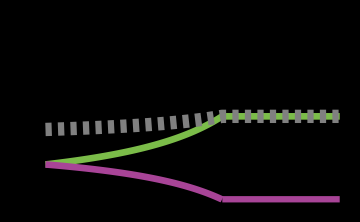

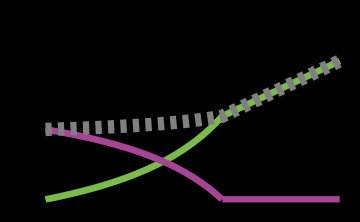

```mathematica
jplot2C=jplot[exampleVals,DIN,jPlotDINmax,{FrameTicks->None,PlotRange->{0,.5}},jPlotQuantitiesC,"F"]
jplot2N=jplot[exampleVals,DIN,jPlotDINmax,{FrameTicks->None,PlotRange->{0,.5}},jPlotQuantitiesN,"I"]
```

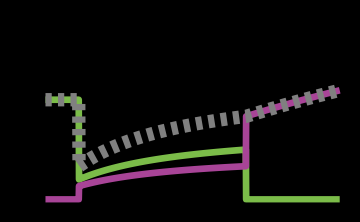

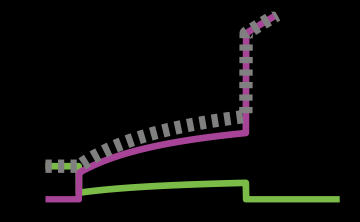

```mathematica
jplot3C=jplot[exampleVals,B,jPlotBmax,{FrameTicks->None,PlotRange->{0,.5}},jPlotQuantitiesC,"E"]
jplot3N=jplot[exampleVals,B,jPlotBmax,{FrameTicks->None,PlotRange->{0,.5}},jPlotQuantitiesN,"H"]
```

```mathematica
(Export[NotebookDirectory[]<>"export/figure2.pdf",#]; #)&@Style[Grid[{{αplotlegend,αplot1,αplot3,αplot2},{jplotlegends[[1]],jplot1C,jplot3C,jplot2C},{jplotlegends[[2]],jplot1N,jplot3N,jplot2N},Style[#,FontFamily->"Arial",labelsize]&/@{"","  Light","     Bacteria","       Dissolved nitrogen"}},Alignment->Center,Spacings->{{2->1,3->-3,4->-3},{2->1,3->1,4->0}}],LineBreakWithin->False]
```

Investments
-Graphics- | Vacuoles, α_V
-Graphics- | Plastids, α_P
-Graphics- | Growth machinery, α_M | -Graphics- | -Graphics- | -Graphics-
Carbon fluxes
-Graphics- | Vacuoles
-Graphics- | Plastids
-Graphics- | Total
-Graphics- | Growth | -Graphics- | -Graphics- | -Graphics-
Nitrogen fluxes
-Graphics- | Vacuoles
-Graphics- | Plastids
-Graphics- | Total
-Graphics- | Growth | -Graphics- | -Graphics- | -Graphics-
 |   Light |      Bacteria |        Dissolved nitrogen